# Check Gibbs sampling

```mathematica
fMakePlots[mode_,iChain_,BP_]:=Module[{data1,dataX1,data11,dataY1,boxLength,plts,data111},
boxLength=40;
plts={{},{}};

SetDirectory[NotebookDirectory[]];
Do[
data1=Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_"<>IntegerString[i,10,1]<>".txt","Table"];
If[BP[[i+1]]=="binary",
data11=ConstantArray[0,{boxLength,boxLength}];
dataX1=Select[data1,StringTake[#[[3]],1]=="X"&][[;;,{1,2}]];
dataY1=Select[data1,StringTake[#[[3]],1]=="Y"&][[;;,{1,2}]];
Do[
data11[[pt[[1]],pt[[2]]]]=Black;
,{pt,dataX1}];
Do[
data11[[pt[[1]],pt[[2]]]]=Blue;
,{pt,dataY1}];

AppendTo[plts[[1]],ArrayPlot[data11,ImageSize->200]];
AppendTo[plts[[2]],Null];
,
data11=ConstantArray[0,{boxLength,boxLength}];
data111=ConstantArray[0,{boxLength,boxLength}];
Do[
data11[[pt[[1]],pt[[2]]]]=Opacity[pt[[4]],Black];
data111[[pt[[1]],pt[[2]]]]=Opacity[pt[[6]],Blue];
,{pt,data1}];

AppendTo[plts[[1]],ArrayPlot[data11,ImageSize->200]];
AppendTo[plts[[2]],ArrayPlot[data111,ImageSize->200]];
];
,{i,0,2}];

Return[
Grid[plts]]
];
```

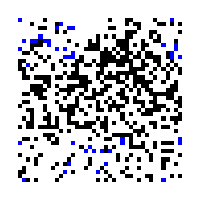
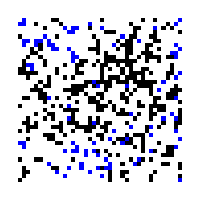
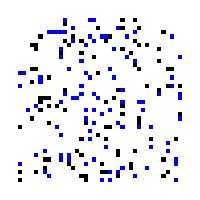
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
fMakePlots["awake",5,{"binary","binary","binary"}]
```

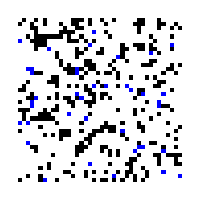
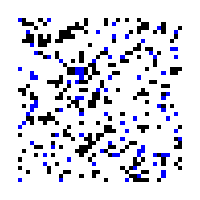
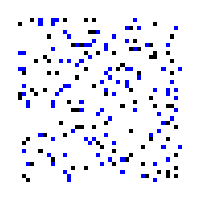
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
fMakePlots["asleep",0,{"binary","binary","binary"}]
```

# Check moments (biases)

```mathematica
fGetMoments[mode_,iChain_,BP_]:=Module[{data1,dataX1,dataY1,boxLength,plts},
boxLength=40;
plts={{},{}};

SetDirectory[NotebookDirectory[]];
Do[
data1=Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_"<>IntegerString[i,10,1]<>".txt","Table"];
If[BP[[i+1]]=="binary",
dataX1=Select[data1,StringTake[#[[3]],1]=="X"&][[;;,{1,2}]];
dataY1=Select[data1,StringTake[#[[3]],1]=="Y"&][[;;,{1,2}]];

AppendTo[plts[[1]],Length[dataX1]];
AppendTo[plts[[2]],Length[dataY1]];
,

AppendTo[plts[[1]],Total[data1[[;;,4]]]];
AppendTo[plts[[2]],Total[data1[[;;,6]]]];
];
,{i,0,2}];

Return[
Grid[plts]]
];
```

```mathematica
fGetMoments["awake",8,{"binary","binary","binary"}]
```

202 | 160 | 91
21 | 73 | 103

```mathematica
fGetMoments["asleep",5,{"binary","binary","binary"}]
```

360 | 301 | 98
57 | 116 | 101

# Check moments (weights)

### Adjacency matrix

```mathematica
boxLength=40;
adj={};
Do[
Do[
idx1=(i1-1)*boxLength+j1;

Do[
Do[
i2=i1+i1Plus;
j2=j1+j1Plus;
If[i2>boxLength,i2-=boxLength];
If[j2>boxLength,j2-=boxLength];
idx2=(i2-1)*boxLength+j2;
AppendTo[adj,{idx1,idx2}->1];
,{j1Plus,0,2}];
,{i1Plus,0,2}];

,{j1,1,boxLength}];
,{i1,1,boxLength}];
adj=SparseArray[adj,{boxLength^2,boxLength^2}];
```

```mathematica
conv[dat_]:=Module[
{datC},
datC=Map[{(#[[1]]-1)*boxLength+#[[2]]}->1&,dat];
Return[SparseArray[datC,{boxLength^2}]];
];
```

### Moments

```mathematica
getMoments[mode_,iChain_,BP_]:=Module[{moments,data0,data1,data2,data0X,data0Y,data1X1,data1Y1,data2X2,data2Y2},
moments=Association[];

SetDirectory[NotebookDirectory[]];

If[BP[[1]]=="binary",
data0=Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_0.txt","Table"];
data0X=conv[Select[data0,#[[3]]=="X"&]];
data0Y=conv[Select[data0,#[[3]]=="Y"&]];
,
data0=Transpose[Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_0.txt","Table"]];
data0X=data0[[4]];
data0Y=data0[[6]];
];
If[BP[[1]]=="binary",
data1=Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_1.txt","Table"];
data1X1=conv[Select[data1,#[[3]]=="X1"&]];
data1Y1=conv[Select[data1,#[[3]]=="Y1"&]];
,
data1=Transpose[Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_1.txt","Table"]];
data1X1=data1[[4]];
data1Y1=data1[[6]];
];
If[BP[[1]]=="binary",
data2=Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_2.txt","Table"];
data2X2=conv[Select[data2,#[[3]]=="X2"&]];
data2Y2=conv[Select[data2,#[[3]]=="Y2"&]];
,
data2=Transpose[Import["../data/diagnose_sampling/"<>mode<>"_chain_"<>IntegerString[iChain,10,2]<>"_layer_2.txt","Table"]];
data2X2=data2[[4]];
data2Y2=data2[[6]];
];

moments["hX"]=Total[data0X];
moments["hY"]=Total[data0Y];
moments["wXX1"]=data0X.adj.data1X1;
moments["wYY1"]=data0Y.adj.data1Y1;
moments["bX1"]=Total[data1X1];
moments["bY1"]=Total[data1Y1];
moments["wX1X2"]=data1X1.adj.data2X2;
moments["wY1Y2"]=data1Y1.adj.data2Y2;
moments["bX2"]=Total[data2X2];
moments["bY2"]=Total[data2Y2];

Return[moments];
]
```

```mathematica
momentsAwake=Association[];
Do[
momentsAwake[theta]={};
,{theta,{"wX1X2","wY1Y2","wXX1","wYY1"}}];
Do[
moms=getMoments["awake",iChain,{"binary","binary","binary"}];
Do[
AppendTo[momentsAwake[theta],moms[theta]];
,{theta,{"wX1X2","wY1Y2","wXX1","wYY1"}}];
,{iChain,0,9}];
```

```mathematica
momentsAwake
```

<|wX1X2→{89,67,165,123,103,188,171,132,89,89},wY1Y2→{33,59,86,36,35,50,26,58,44,46},wXX1→{288,202,2027,742,333,1563,929,820,337,688},wYY1→{19,98,500,9,6,104,21,71,30,20}|>

```mathematica
momentsAsleep=Association[];
Do[
momentsAsleep[theta]={};
,{theta,{"wX1X2","wY1Y2","wXX1","wYY1"}}];
Do[
moms=getMoments["asleep",iChain,{"binary","binary","binary"}];
Do[
AppendTo[momentsAsleep[theta],moms[theta]];
,{theta,{"wX1X2","wY1Y2","wXX1","wYY1"}}];
,{iChain,0,9}];
```

```mathematica
momentsAsleep
```

<|wX1X2→{122,123,166,143,167,144,109,151,122,128},wY1Y2→{48,73,71,72,56,61,91,46,63,46},wXX1→{825,1032,1195,937,1068,1015,573,859,1018,914},wYY1→{67,124,151,109,282,186,300,115,118,44}|>

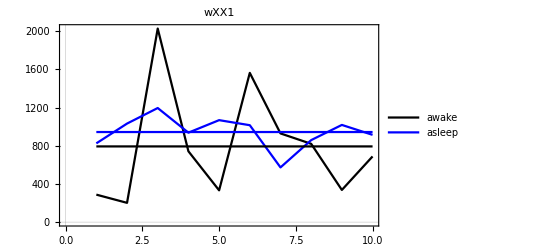
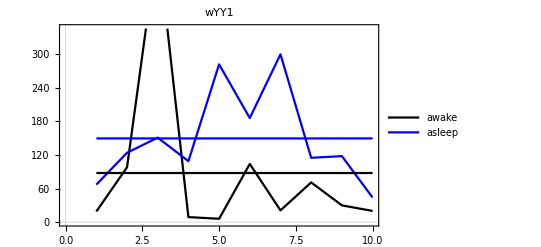
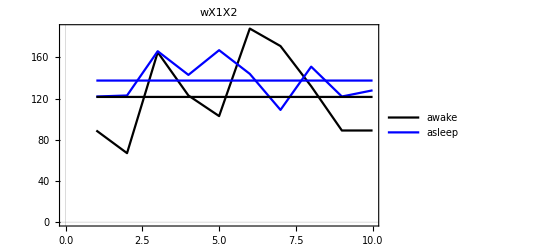
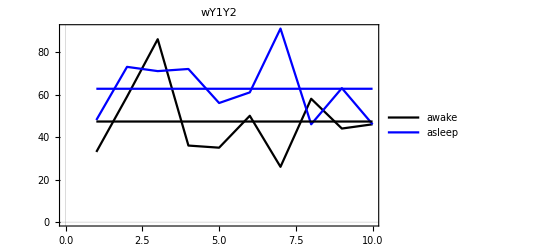

```mathematica
Row[
Table[
ListLinePlot[{momentsAwake[theta],momentsAsleep[theta],{{1,Mean[momentsAwake[theta]]},{10,Mean[momentsAwake[theta]]}},{{1,Mean[momentsAsleep[theta]]},{10,Mean[momentsAsleep[theta]]}}},PlotLegends->{"awake","asleep"},PlotStyle->{Black,Blue,Black,Blue},PlotLabel->theta]
,{theta,{"wXX1","wYY1","wX1X2","wY1Y2"}}]
]
```